# Conceptual model

### Model equations

```mathematica
Clear[s,cal,cau,cst,hmax,rmax,shh,m,ma,mh,k, alpha,hcal,pdal,peal,pbal,beta,pdau,peau,pbau,pdst]
ds = rmax*s*(1-s/k)-s*(m+ma+mh*hmax*shh/(shh+s));
dcal = alpha*hcal/(hcal+(hmax*shh/(shh+s)))-cal*(pdal+peal+pbal);
dcau =beta*s-cau*(pdau+peau+pbau);
dcst = pbal*cal+pbau*cau-pdst*cst;
```

### Equilibria

```mathematica
sol = Simplify[Solve[{ds==0},{s}]]
```

{{s→0},{s→(-k m-k ma+k rmax-rmax shh+√(-4 k (m+ma+hmax mh-rmax) rmax shh+(k (m+ma-rmax)+rmax shh)^2))/(2 rmax)},{s→-(k m+k ma-k rmax+rmax shh+√(-4 k (m+ma+hmax mh-rmax) rmax shh+(k (m+ma-rmax)+rmax shh)^2))/(2 rmax)}}

The ecological dynamics exhibits three equilibria.

```mathematica
FullSimplify[Solve[dcal==0&& dcau==0 && dcst==0, {cal,cau,cst}]]
```

{{cal→(alpha hcal (s+shh))/((pbal+pdal+peal) (hmax shh+hcal (s+shh))),cau→(beta s)/(pbau+pdau+peau),cst→((beta pbau s)/(pbau+pdau+peau)+(alpha hcal pbal (s+shh))/((pbal+pdal+peal) (hmax shh+hcal (s+shh))))/pdst}}

The biogeochemical dynamics exhibits one equilibria.

### Equilibria feasibility

Equilibria are feasible if they are greater than or equal to zero.

#### First equilibrium

Parameter assumptions:

```mathematica
assumptions=And[rmax>0,k>0,shh>0,m>0,m<=1,ma>0,ma<=1,mh>0,mh<=1];
```

First equilibrium does exist if:

```mathematica
Assuming[assumptions, FullSimplify[sol[[1]][[1]][[2]]>=0]] (*we look for conditions where the equilibrium is greater than or equal to zero given the parameter assumptions*)
```

True

First equilibrium is always feasible .

Determine when equilibrium is stable before plotting it:

```mathematica
(D[rmax*s*(1-s/k)-s*(m+ma+mh*hmax*shh/(shh+s)),s]/.sol[[1]][[1]])<=0
```

-m-ma-hmax mh+rmax≤0

#### Second equilibrium

Second equilibrium does exist if:

```mathematica
Assuming[assumptions, FullSimplify[sol[[2]][[1]][[2]]>=0]](*we look for conditions where the equilibrium is greater than or equal to zero given the parameter assumptions*)
```

√(-4 k (m+ma+hmax mh-rmax) rmax shh+(k (m+ma-rmax)+rmax shh)^2)≥k (m+ma-rmax)+rmax shh

#### Third equilibrium

Third equilibrium does exist if:

```mathematica
Assuming[assumptions, FullSimplify[sol[[3]][[1]][[2]]>=0 ]] (*we look for conditions where the equilibrium is greater than or equal to zero given the parameter assumptions*)
```

k (m+ma)+rmax shh+√(-4 k (m+ma+hmax mh-rmax) rmax shh+(k (m+ma-rmax)+rmax shh)^2)≤k rmax

#### Coexistence of equilibria

All equilibria coexist if:

```mathematica
reducedResult=TimeConstrained[Reduce[sol[[3]][[1]][[2]]>0&&sol[[2]][[1]][[2]]>0&&assumptions],600]; (*we look for conditions where the equilibria are greater than or equal to zero given the parameter assumptions*)
simplifiedResult=Simplify[LogicalExpand[reducedResult&&assumptions],assumptions] (*we simplify as much as possible*)
```

k>-(rmax shh)/(m+ma-rmax)&&rmax>m+ma&&rmax<m+ma+hmax mh&&2 k (m+ma+2 hmax mh-rmax) rmax shh≤k^2 (m+ma-rmax)^2+rmax^2 shh^2

In order to determine which equilibrium corresponds to what, we look at which equilibrium is greater under coexistence conditions:

```mathematica
Assuming[k>-(rmax shh)/(m+ma-rmax)&&rmax>m+ma&&rmax<m+ma+hmax mh&&2 k (m+ma+2 hmax mh-rmax) rmax shh≤k^2 (m+ma-rmax)^2+rmax^2 shh^2&& assumptions, FullSimplify[sol[[3]][[1]][[2]]<sol[[2]][[1]][[2]] ]]
```

√(-4 k (m+ma+hmax mh-rmax) rmax shh+(k (m+ma-rmax)+rmax shh)^2)>0

This is always true so the second equilibrium is the seagrass equilibrium, and the third equilibrium is the unstable equilibrium .

### Bifurcation diagrams

#### Ecological dynamics

```mathematica
seagrassColor=Darker[Green,0.5]; (*color of the seagrass stable equilibrium*)
bistableColor=Directive[Dotted,Black,Dashing[{0.01}]]; (*color of the unstable equilibrium*)
bareColor=Darker[Yellow]; (*color of the bare stable equilibrium*)

(*parameter values*)
rmax=1.2;
k=5.5;
mh=0.05;
shh=1;
hmax=15;
m = 0.01;

seagrass=If[Im[(-k m-k ma+k rmax-rmax shh+√(-4 k (m+ma+hmax mh-rmax) rmax shh+(k (m+ma-rmax)+rmax shh)^2))/(2 rmax)]==0&& (*to avoid problems of imaginary solutions*)(-k m-k ma+k rmax-rmax shh+√(-4 k (m+ma+hmax mh-rmax) rmax shh+(k (m+ma-rmax)+rmax shh)^2))/(2 rmax)>0,(*if seagrass equilibrium exists we plot it*)(-k m-k ma+k rmax-rmax shh+√(-4 k (m+ma+hmax mh-rmax) rmax shh+(k (m+ma-rmax)+rmax shh)^2))/(2 rmax),None]; 

bistable=If[Im[-(k m+k ma-k rmax+rmax shh+√(-4 k (m+ma+hmax mh-rmax) rmax shh+(k (m+ma-rmax)+rmax shh)^2))/(2 rmax)]==0&& (*to avoid problems of imaginary solutions*)-(k m+k ma-k rmax+rmax shh+√(-4 k (m+ma+hmax mh-rmax) rmax shh+(k (m+ma-rmax)+rmax shh)^2))/(2 rmax)>0, (*if bistable equilibrium exists we plot it*)-(k m+k ma-k rmax+rmax shh+√(-4 k (m+ma+hmax mh-rmax) rmax shh+(k (m+ma-rmax)+rmax shh)^2))/(2 rmax),None]; 

bare=If[-m-ma-hmax mh+rmax≤0,0,None]; (*if bare equilibrium is stable we plot it*)

plot=Show[Plot[seagrass,{ma,0,1},PlotStyle->seagrassColor],Plot[bistable,{ma,0,1},PlotStyle->bistableColor],Plot[bare,{ma,0,1},PlotStyle->bareColor],Frame->True,FrameLabel->{Row[{Style["Anthropogenic mortality rate ",16,Black],Style[Subscript["m","A"],16,Black], Style[Superscript[" (day",-1], 16, Black],  Style[")",16,Black]}],Row[{Style["Seagrass biomass",16,Black], Style[" (g DW",16,Black], Style[Superscript[" m",-2], 16, Black], Style[")",16,Black]}]}
,FrameTicks->{{{0,1,2,3,4,5},None},{{0,0.25,0.5,0.75,1},None}},FrameTicksStyle->Directive[FontSize->14],Axes->False,PlotRange->{{0,1},{0,5}},AspectRatio->0.8,ImageSize->{1000,500}]; 

plot=Legended[plot,Placed[LineLegend[{seagrassColor,bistableColor,bareColor},{Style["Seagrass",16,Black],Style["Bistable",16,Black],Style["Bare",16,Black]},LegendLayout->{"Column",1},LegendFunction->None,LegendMargins->5, LabelStyle->{FontSize->16},LegendMarkerSize->20],{1.05,0.5}]]
```

-Graphics-

```mathematica
Export["",plot,ImageResolution->1000];(*set your own working directory*)
```

#### Biogeochemical dynamics

We plot each carbon compartment separately and then merge them.

ALLOCHTHONOUS CARBON
We incorporate each ecological equilibrium into the allochthonous carbon equilibrium:

```mathematica
plot2=Module[{seagrassColor,bistableColor,bareColor,seagrass,bistable,bare,rmax,k,mh,shh,hmax,m,ma,pdal,peal,pbal,alpha,hcal},

seagrassColor=Darker[Orange];(*color of the seagrass stable equilibrium*)
bistableColor=Directive[Dotted,Darker[Orange],Dashing[{0.01}]];(*color of the unstable equilibrium*)
bareColor=Darker[Orange];(*color of the bare stable equilibrium*)

(*parameter values*)
rmax=1.2;
k=5.5;
mh=0.05;
shh=1;
hmax=15;
m = 0.01;
pdal=0.05;
peal=0.2;
pbal=0.01;
alpha=4;
hcal=10;

seagrass=If[Im[(-k m-k ma+k rmax-rmax shh+√(-4 k (m+ma+hmax mh-rmax) rmax shh+(k (m+ma-rmax)+rmax shh)^2))/(2 rmax)]==0&& (*to avoid problems of imaginary solutions*)(-k m-k ma+k rmax-rmax shh+√(-4 k (m+ma+hmax mh-rmax) rmax shh+(k (m+ma-rmax)+rmax shh)^2))/(2 rmax)>0,(*if ecological seagrass equilibrium exists we plot the corresponding Cal equilibrium*)1/(pdal+peal+pbal)*(alpha*hcal/(hcal+hmax*shh/(shh+(-k m-k ma+k rmax-rmax shh+Sqrt[-4 k (m+ma+hmax mh-rmax) rmax shh+(k (m+ma-rmax)+rmax shh)^2])/(2 rmax)))),None];

bistable=If[(Im[-(k m+k ma-k rmax+rmax shh+√(-4 k (m+ma+hmax mh-rmax) rmax shh+(k (m+ma-rmax)+rmax shh)^2))/(2 rmax)]==0)&& (*to avoid problems of imaginary solutions*)-(k m+k ma-k rmax+rmax shh+√(-4 k (m+ma+hmax mh-rmax) rmax shh+(k (m+ma-rmax)+rmax shh)^2))/(2 rmax)>0,(*if ecological bistable equilibrium exists we plot the corresponding Cal equilibrium*)1/(pdal+peal+pbal)*(alpha*hcal/(hcal+hmax*shh/(shh+-((k m+k ma-k rmax+rmax shh+Sqrt[-4 k (m+ma+hmax mh-rmax) rmax shh+(k (m+ma-rmax)+rmax shh)^2])/(2 rmax))))),None];

bare=If[-m-ma-hmax mh+rmax≤0,1/(pdal+peal+pbal)*(alpha*hcal/(hcal+hmax*shh/(shh))),None]; (*if ecological bare equilibrium is stable we plot the corresponding Cal equilibrium*)

plot22=Show[Plot[seagrass,{ma,0,1},PlotStyle->seagrassColor],Plot[bistable,{ma,0,1},PlotStyle->bistableColor],Plot[bare,{ma,0,1},PlotStyle->bareColor],Frame->True,FrameLabel->{"",None},FrameTicks->{{{{0,"0"},{5,"5"},{10,"10"},{15,"15"},{20,"20"}},None},{{{0,"0"},{0.25,"0.25"},{0.5,"0.5"},{0.75,"0.75"},{1,"1"}},None}},FrameTicksStyle->Directive[FontSize->14],Axes->False,PlotRange->{{0,1},{0,20}},ImageSize->{1000,500}]];

Legended[plot22,Placed[LineLegend[{Darker[Orange],bistableColor,bareColor},{"Allochthonous"},LegendLayout->{"Column",1},LegendFunction->None,LegendMargins->5],{1.05,0.5}]]
```

-Graphics-

AUTOCHTHONOUS CARBON
We incorporate each ecological equilibrium into the autochthonous carbon equilibrium:

```mathematica
plot3=Module[{seagrassColor,bistableColor,bareColor,seagrass,bistable,bare,rmax,k,mh,shh,hmax,m,ma,pdau,peau,pbau,beta},

seagrassColor=Red;(*color of the seagrass stable equilibrium*)
bistableColor=Directive[Dotted,Red,Dashing[{0.01}]];(*color of the unstable equilibrium*)
bareColor=Red;(*color of the bare stable equilibrium*)

(*parameter values*)
rmax=1.2;
k=5.5;
mh=0.05;
shh=1;
hmax=15;
m = 0.01;
beta=0.6;
pbau=0.01;
peau=0.2;
pdau=0.05;

seagrass=If[Im[(-k m-k ma+k rmax-rmax shh+√(-4 k (m+ma+hmax mh-rmax) rmax shh+(k (m+ma-rmax)+rmax shh)^2))/(2 rmax)]==0&& (*to avoid problems of imaginary solutions*)(-k m-k ma+k rmax-rmax shh+√(-4 k (m+ma+hmax mh-rmax) rmax shh+(k (m+ma-rmax)+rmax shh)^2))/(2 rmax)>0,(*if ecological seagrass equilibrium exists we plot the corresponding Cau equilibrium*)beta*(-k m-k ma+k rmax-rmax shh+Sqrt[-4 k (m+ma+hmax mh-rmax) rmax shh+(k (m+ma-rmax)+rmax shh)^2])/(2 rmax)/(pdau+peau+pbau),None];

bistable=If[(Im[-(k m+k ma-k rmax+rmax shh+√(-4 k (m+ma+hmax mh-rmax) rmax shh+(k (m+ma-rmax)+rmax shh)^2))/(2 rmax)]==0)&& (*to avoid problems of imaginary solutions*)-(k m+k ma-k rmax+rmax shh+√(-4 k (m+ma+hmax mh-rmax) rmax shh+(k (m+ma-rmax)+rmax shh)^2))/(2 rmax)>0,(*if ecological bistable equilibrium exists we plot the corresponding Cau equilibrium*)beta*-((k m+k ma-k rmax+rmax shh+Sqrt[-4 k (m+ma+hmax mh-rmax) rmax shh+(k (m+ma-rmax)+rmax shh)^2])/(2 rmax))/(pdau+peau+pbau),None];

bare=If[-m-ma-hmax mh+rmax≤0,0,None]; (*if ecological bare equilibrium is stable we plot the corresponding Cal equilibrium*)

plot33=Show[Plot[seagrass,{ma,0,1},PlotStyle->seagrassColor],Plot[bistable,{ma,0,1},PlotStyle->bistableColor],Plot[bare,{ma,0,1},PlotStyle->bareColor],Frame->True,FrameLabel->{"",None},FrameTicks->{{{{0,"0"},{5,"5"},{10,"10"},{15,"15"},{20,"20"}},None},{{{0,"0"},{0.25,"0.25"},{0.5,"0.5"},{0.75,"0.75"},{1,"1"}},None}},FrameTicksStyle->Directive[FontSize->14],Axes->False,PlotRange->{{0,1},{0,20}},ImageSize->{1000,500}]];

Legended[plot33,Placed[LineLegend[{Red},{"Autochthonous"},LegendLayout->{"Column",1},LegendFunction->None,LegendMargins->5],{1.05,0.5}]]
```

-Graphics-

STABLE CARBON
We incorporate each ecological equilibrium into the stable carbon equilibrium:

```mathematica
plot4=Module[{seagrassColor,bistableColor,bareColor,seagrass,bistable,bare,rmax,k,mh,shh,hmax,m,ma,pdal,peal,pbal,alpha,hcal, pdau,peau,pbau,beta, pdst},

seagrassColor=Purple; (*color of the seagrass stable equilibrium*)
bistableColor=Directive[Dotted,Purple,Dashing[{0.01}]]; (*color of the unstable equilibrium*)
bareColor=Purple; (*color of the bare stable equilibrium*)

(*parameter values*)
rmax=1.2;
k=5.5;
mh=0.05;
shh=1;
hmax=15;
m = 0.01;
pdal=0.05;
peal=0.2;
pbal=0.01;
alpha=4;
hcal=10;
beta=0.6;
pbau=0.01;
peau=0.2;
pdau=0.05;
pdst=0.014;

seagrass=If[Im[(-k m-k ma+k rmax-rmax shh+√(-4 k (m+ma+hmax mh-rmax) rmax shh+(k (m+ma-rmax)+rmax shh)^2))/(2 rmax)]==0&& (*to avoid problems of imaginary solutions*)(-k m-k ma+k rmax-rmax shh+√(-4 k (m+ma+hmax mh-rmax) rmax shh+(k (m+ma-rmax)+rmax shh)^2))/(2 rmax)>0,(*if ecological seagrass equilibrium exists we plot the corresponding Cst equilibrium*)(pbal*1/(pdal+peal+pbal)*(alpha*hcal/(hcal+hmax*shh/(shh+(-k m-k ma+k rmax-rmax shh+Sqrt[-4 k (m+ma+hmax mh-rmax) rmax shh+(k (m+ma-rmax)+rmax shh)^2])/(2 rmax))))+pbau*beta*(-k m-k ma+k rmax-rmax shh+Sqrt[-4 k (m+ma+hmax mh-rmax) rmax shh+(k (m+ma-rmax)+rmax shh)^2])/(2 rmax)/(pdau+peau+pbau))/pdst,None];

bistable=If[(Im[-(k m+k ma-k rmax+rmax shh+√(-4 k (m+ma+hmax mh-rmax) rmax shh+(k (m+ma-rmax)+rmax shh)^2))/(2 rmax)]==0)&& (*to avoid problems of imaginary solutions*)-(k m+k ma-k rmax+rmax shh+√(-4 k (m+ma+hmax mh-rmax) rmax shh+(k (m+ma-rmax)+rmax shh)^2))/(2 rmax)>0,(*if ecological bistable equilibrium exists we plot the corresponding Cst equilibrium*)(pbal*1/(pdal+peal+pbal)*(alpha*hcal/(hcal+hmax*shh/(shh+-((k m+k ma-k rmax+rmax shh+Sqrt[-4 k (m+ma+hmax mh-rmax) rmax shh+(k (m+ma-rmax)+rmax shh)^2])/(2 rmax)))))+pbau*beta*-((k m+k ma-k rmax+rmax shh+Sqrt[-4 k (m+ma+hmax mh-rmax) rmax shh+(k (m+ma-rmax)+rmax shh)^2])/(2 rmax))/(pdau+peau+pbau))/pdst,None];

bare=If[-m-ma-hmax mh+rmax≤0,pbal*1/(pdal+peal+pbal)*(alpha*hcal/(hcal+hmax*shh/(shh)))/pdst,None]; (*if ecological bare equilibrium is stable we plot the corresponding Cst equilibrium*)

plot44=Show[Plot[seagrass,{ma,0,1},PlotStyle->seagrassColor],Plot[bistable,{ma,0,1},PlotStyle->bistableColor],Plot[bare,{ma,0,1},PlotStyle->bareColor],Frame->True,FrameLabel->{"",None},FrameTicks->{{{{0,"0"},{5,"5"},{10,"10"},{15,"15"},{20,"20"}},None},{{{0,"0"},{0.25,"0.25"},{0.5,"0.5"},{0.75,"0.75"},{1,"1"}},None}},FrameTicksStyle->Directive[FontSize->14],Axes->False,PlotRange->{{0,1},{0,20}},ImageSize->{1000,500}]];

Legended[plot44,Placed[LineLegend[{Purple},{"Stable"},LegendLayout->{"Column",1},LegendFunction->None,LegendMargins->5],{1.05,0.5}]]
```

-Graphics-

```mathematica
mergedPlot=Show[Legended[plot22,Placed[LineLegend[{Darker[Orange],bistableColor,bareColor},{Style["Allochthonous (\!\(\*SubscriptBox[\(C\), \(At\)]\))",16,Black]},LegendLayout->{"Column",1},LegendFunction->None,LegendMargins->5],{1.05,0.5}]],Legended[plot33,Placed[LineLegend[{Red},{Style["Autochthonous (\!\(\*SubscriptBox[\(C\), \(Au\)]\))",16,Black]},LegendLayout->{"Column",1},LegendFunction->None,LegendMargins->5],{1.05,0.5}]],Legended[plot44,Placed[LineLegend[{Purple},{Style["Stable (\!\(\*SubscriptBox[\(C\), \(St\)]\))",16,Black]},LegendLayout->{"Column",1},LegendFunction->None,LegendMargins->5],{1.05,0.5}]],PlotRange->{{0,1},{0,20}},AspectRatio->0.8,ImageSize->{1000,500},FrameLabel->{Row[{Style["Anthropogenic mortality rate ",16,Black],Style[Subscript["m","A"],16,Black], Style[Superscript[" (day",-1], 16, Black],  Style[")",16,Black]}],Row[{Style["Carbon mass",16,Black], Style[" (g DW",16,Black], Style[Superscript[" m",-2], 16, Black], Style[")",16,Black]}]}]
```

-Graphics-

```mathematica
Export["",mergedPlot,ImageResolution->1000]; (*set your own working directory*)
```

### Eigenvalues of ecological dynamics

#### Derivative/Jacobian matrix

```mathematica
J=D[ds,s](*For a 1D system, the Jacobian matrix is the derivative*)
```

-m-ma-(rmax s)/k+rmax (1-s/k)+(hmax mh s shh)/(s+shh)^2-(hmax mh shh)/(s+shh)

#### Eigenvalues/Jacobian at equilibria

```mathematica
eigenvalues = J/.sol; (*For a 1D system,the eigenvalue is the Jacobian (derivative) evaluated at the equilibrium point*)
```

```mathematica
{eigenvalues[[1]],eigenvalues[[2]]} (*Eigenvalues of the two stable equilibria*)
```

{-m-ma-hmax mh+rmax,-m-ma-(-k m-k ma+k rmax-rmax shh+√(-4 k (m+ma+hmax mh-rmax) rmax shh+(k (m+ma-rmax)+rmax shh)^2))/(2 k)+(hmax mh shh (-k m-k ma+k rmax-rmax shh+√(-4 k (m+ma+hmax mh-rmax) rmax shh+(k (m+ma-rmax)+rmax shh)^2)))/(2 rmax (shh+(-k m-k ma+k rmax-rmax shh+√(-4 k (m+ma+hmax mh-rmax) rmax shh+(k (m+ma-rmax)+rmax shh)^2))/(2 rmax))^2)-(hmax mh shh)/(shh+(-k m-k ma+k rmax-rmax shh+√(-4 k (m+ma+hmax mh-rmax) rmax shh+(k (m+ma-rmax)+rmax shh)^2))/(2 rmax))+rmax (1-(-k m-k ma+k rmax-rmax shh+√(-4 k (m+ma+hmax mh-rmax) rmax shh+(k (m+ma-rmax)+rmax shh)^2))/(2 k rmax))}

#### Eigenvalues as a function of mA

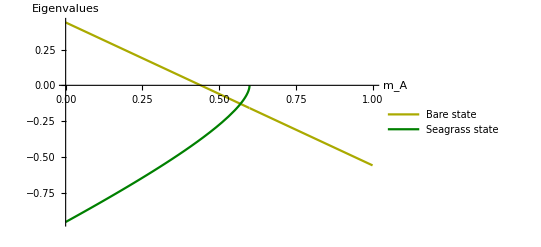

```mathematica
rmax=1.2;
k=5.5;
mh=0.05;
shh=1;
hmax=15;
m = 0.01;
eigenplot =Plot[{eigenvalues[[1]], eigenvalues[[2]]},{ma,0,1},PlotLegends->{"Bare state","Seagrass state"},AxesLabel->{Style[Subscript["m","A"],12,Black],Style["Eigenvalues",12,Black]},PlotStyle->{Darker[Yellow],Darker[Green,0.5]},PlotRange->All]
```

```mathematica
Export["",eigenplot,ImageResolution->1000]; (*set your own working directory*)
```